Вычисление n для метода прямоугольников

```mathematica
f[t_]=Exp[t]*Log[t+2];
```

```mathematica
Plot[f[t],{t,1,2}, Frame->True,GridLines->Automatic, FrameLabel->{"t", "f(t)"}]
```

График второй производной

```mathematica
Plot[f''[t],{t,1,2}, Frame->True,GridLines->Automatic, FrameLabel->{"t", "f(t)"}]
```

```mathematica
m=MaxValue[{f''[x],1<=x<=2},x]//N;
```

```mathematica
n=1;
```

```mathematica
While[(m*(2-1)^3)/(24*n^2)>10^-4,n++]
```

```mathematica
n
```

75

Вычисление n  для метода Симпсона

График четвертой производной

```mathematica
Plot[f''''[t],{t,1,2}, Frame->True,GridLines->Automatic, FrameLabel->{"t", "f(t)"}]
```

```mathematica
mm=MaxValue[{f''''[x],1<=x<=2},x]//N;
```

```mathematica
n=1;
```

```mathematica
While[mm/(90*n^4)*((2-1)/2)^5>10^-4,n++]
```

```mathematica
n
```

3

Вычисление количества элементов методом прямоугольников

```mathematica
f[t_]:=0.08*t-((2^t+1)^2)/(100^2*2);
```

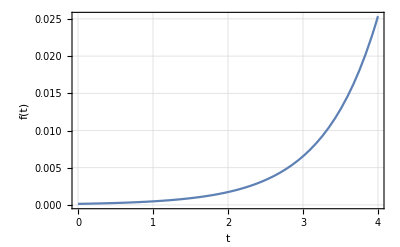

```mathematica
Plot[-f''[t],{t,0,4}, Frame->True,GridLines->Automatic, FrameLabel->{"t", "f(t)"}]
```

```mathematica
mm=MaxValue[{-f''[x],0<=x<=4},x]//N;
```

```mathematica
n=1;
b = 3.5;
```

```mathematica
While[(b-0)^3/(12*n^4)*mm>10^-2,n++]
```

```mathematica
n
```

2

```mathematica
Integrate[f[t],{t,0,4}]
```

0.628439